{0,0,10,12,30,24,20,18,19,15,0,0,0,2}

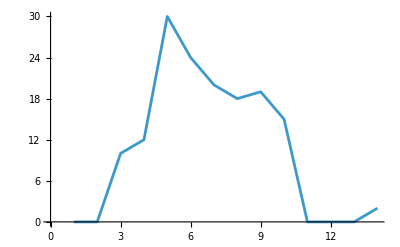

```mathematica
l1={0,0,10,12,30,24,20,18,19,15,0,0,0,2}
ListLinePlot[l1]
```

```mathematica
cwt=ContinuousWaveletTransform[l1,MexicanHatWavelet[1],{3,4}]
```

ContinuousWaveletData[…]

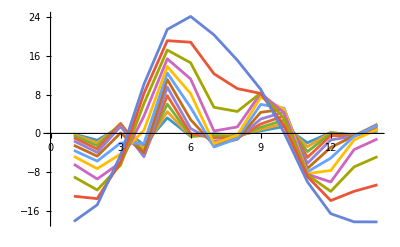

```mathematica
ListLinePlot[cwt[All,"Values"]]
```

```mathematica
cwt[All,"Values"]//Dimensions
```

{12,14}

{0,0,10,12,30,40,60,100,110,111}

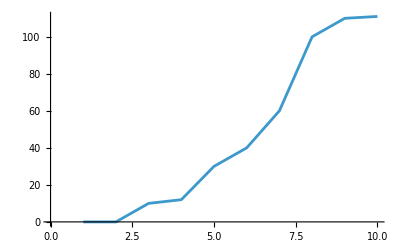

```mathematica
l2={0,0,10,12,30,40,60,100,110,111}
ListLinePlot[l2]
```

```mathematica
cwt2=ContinuousWaveletTransform[l2,MexicanHatWavelet[1],{3,4}]
```

ContinuousWaveletData[…]

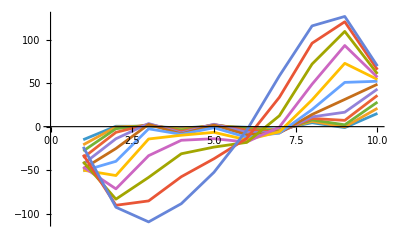

```mathematica
ListLinePlot[cwt2[All,"Values"]]
```

{0.890074,0.545668,0.506917,0.5318,0.591872,0.549856,0.636729,0.911465,0.121013,0.239946}

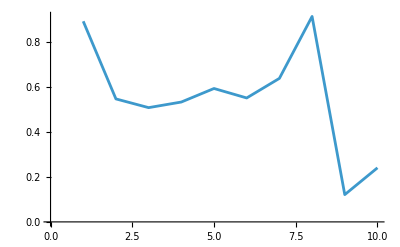

```mathematica
lr=Table[RandomReal[],{10}]
ListLinePlot[lr]
```

```mathematica
cwtr=ContinuousWaveletTransform[lr,MexicanHatWavelet[1]]
```

ContinuousWaveletData[…]

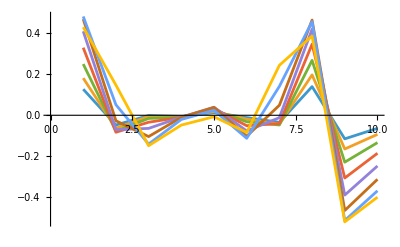

```mathematica
ListLinePlot[cwtr[All,"Values"]]
```

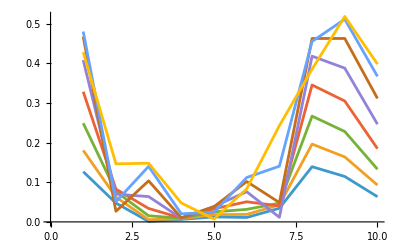

```mathematica
Map[Abs,cwtr[All,"Values"]]//ListLinePlot
```

```mathematica
Map[Norm,cwtr[All,"Values"],{-1}]//ListLinePlot
```

-Graphics-

```mathematica
Map[Re,cwtr[All,"Values"],{-1}]//ListLinePlot
```

-Graphics-

ピーク推定

関数：

```mathematica
ternarize[x_/;x>0]:=1
ternarize[x_/;x==0]:=0
ternarize[x_/;x<0]:=-1
```

```mathematica
bothsidecut[l_]:=l[[2;;-2]]
```

適応：

```mathematica
Map[ternarize,Map[Re,cwtr[All,"Values"],{-1}],{-1}]
```

{{1,-1,-1,-1,1,-1,-1,1,-1,-1},{1,-1,-1,-1,1,-1,-1,1,-1,-1},{1,-1,-1,-1,1,-1,-1,1,-1,-1},{1,-1,-1,-1,1,-1,-1,1,-1,-1},{1,-1,-1,-1,1,-1,-1,1,-1,-1},{1,-1,-1,-1,1,-1,1,1,-1,-1},{1,1,-1,-1,1,-1,1,1,-1,-1},{1,1,-1,-1,-1,-1,1,1,-1,-1}}

```mathematica
Map[ternarize,Map[Re,cwtr[All,"Values"],{-1}],{-1}]//Length
```

8

```mathematica
tmp=Apply[Plus,Map[ternarize,Map[Re,cwtr[All,"Values"],{-1}],{-1}]]//bothsidecut
```

{-4,-8,-8,6,-8,-2,8,-8}

```mathematica
Map[#[[1]]&,Split[tmp]]
```

{-4,-8,6,-8,-2,8,-8}

```mathematica
Count[Map[#[[1]]&,Split[tmp]],8]
```

1

モジュール：

```mathematica
Remove[WTPE]
WTPE[wtlv_]:=Module[{basemat,max},
basemat=Map[ternarize,Map[Re,wtlv,{-1}],{-1}];
max=Length[basemat];
Count[Map[#[[1]]&,Split[bothsidecut[Apply[Plus,basemat]]]],max]
]
WTPE[wtlv_,"position"]:=Module[{basemat,max},
basemat=Map[ternarize,Map[Re,wtlv,{-1}],{-1}];
max=Length[basemat];
Position[bothsidecut[Apply[Plus,basemat]],max]+1
]
```

```mathematica
cwtr[All,"Values"]
```

{{0.126776+0. ⅈ,-0.0475014+5.55112×10^-18 ⅈ,-0.00116265-3.26286×10^-18 ⅈ,-0.00626613-2.85951×10^-18 ⅈ,0.012647+5.27942×10^-18 ⅈ,-0.0111809-9.24323×10^-19 ⅈ,-0.0344409-5.27942×10^-18 ⅈ,0.139338+4.3551×10^-18 ⅈ,-0.114674+3.26286×10^-18 ⅈ,-0.0635346-6.12238×10^-18 ⅈ},{0.180555+0. ⅈ,-0.062652+1.11022×10^-17 ⅈ,-0.00568448-6.52573×10^-18 ⅈ,-0.00791605-7.35046×10^-18 ⅈ,0.0181971+1.05588×10^-17 ⅈ,-0.0189383+7.91066×10^-19 ⅈ,-0.0429216-1.05588×10^-17 ⅈ,0.196387+6.07049×10^-18 ⅈ,-0.164086+6.52573×10^-18 ⅈ,-0.0929405-1.06133×10^-17 ⅈ},{0.249059+0. ⅈ,-0.0766115+2.22045×10^-17 ⅈ,-0.0154533-1.30515×10^-17 ⅈ,-0.0091872-1.47009×10^-17 ⅈ,0.0252379+2.11177×10^-17 ⅈ,-0.0315911+1.58213×10^-18 ⅈ,-0.0473111-2.11177×10^-17 ⅈ,0.267047+1.2141×10^-17 ⅈ,-0.228127+1.30515×10^-17 ⅈ,-0.133062-2.12266×10^-17 ⅈ},{0.328706+0. ⅈ,-0.082667+2.22045×10^-17 ⅈ,-0.0338967-1.30515×10^-17 ⅈ,-0.00955654-1.47009×10^-17 ⅈ,0.0329817+2.11177×10^-17 ⅈ,-0.0507898+1.58213×10^-18 ⅈ,-0.0403748-2.11177×10^-17 ⅈ,0.345663+1.2141×10^-17 ⅈ,-0.305163+1.30515×10^-17 ⅈ,-0.184903-2.12266×10^-17 ⅈ},{0.408382+0. ⅈ,-0.0700257+4.44089×10^-17 ⅈ,-0.063913+0. ⅈ,-0.00914631-2.6139×10^-17 ⅈ,0.0389888+0. ⅈ,-0.0762608-2.11516×10^-18 ⅈ,-0.0116401+0. ⅈ,0.418422+2.95614×10^-17 ⅈ,-0.388126+0. ⅈ,-0.246681-4.57162×10^-17 ⅈ},{0.467641+0. ⅈ,-0.0267776+4.44089×10^-17 ⅈ,-0.103665-2.61029×10^-17 ⅈ,-0.0104802-2.94018×10^-17 ⅈ,0.0383104+4.22354×10^-17 ⅈ,-0.101986+3.16426×10^-18 ⅈ,0.0487566-4.22354×10^-17 ⅈ,0.46305+2.4282×10^-17 ⅈ,-0.463136+2.61029×10^-17 ⅈ,-0.311713-4.24533×10^-17 ⅈ},{0.480584+0. ⅈ,0.0509592+4.44089×10^-17 ⅈ,-0.140177-2.61029×10^-17 ⅈ,-0.0204154-2.94018×10^-17 ⅈ,0.0241561+4.22354×10^-17 ⅈ,-0.112046+3.16426×10^-18 ⅈ,0.14061-4.22354×10^-17 ⅈ,0.45558+2.4282×10^-17 ⅈ,-0.511795+2.61029×10^-17 ⅈ,-0.367455-4.24533×10^-17 ⅈ},{0.428577+0. ⅈ,0.146545+4.996×10^-17 ⅈ,-0.14815+5.27942×10^-18 ⅈ,-0.0477284-1.58813×10^-17 ⅈ,-0.0070852+3.26286×10^-18 ⅈ,-0.0834796-8.62267×10^-18 ⅈ,0.242974-3.26286×10^-18 ⅈ,0.385426+2.7087×10^-17 ⅈ,-0.518676-5.27942×10^-18 ⅈ,-0.398402-5.25431×10^-17 ⅈ}}

```mathematica
WTPE[cwtr[All,"Values"]]
```

1

```mathematica
cwt2[All,"Values"]//WTPE
```

1

```mathematica
cwt[All,"Values"]//WTPE
```

2

```mathematica
WTPE[cwt[All,"Values"],"position"]
```

{{5},{9},{10}}

```mathematica
WTPE[cwtr[All,"Values"],"position"]
```

{{8}}